```mathematica
h[x_]:=Piecewise[{{1+c01 x+c02 x^2+c03 x^3, 0≤x≤1}, {c11(x-1)+c12(x-1)^2+c13(x-1)^3, 1<x≤2}, {0, True}}];
f[x_]:=h[Abs[x]];
```

```mathematica
(*Interpolant constraints*)
I1=f[1]
I2=f[2]
```

1+c01+c02+c03

c11+c12+c13

```mathematica
(*Partition of unity and gradient representation*)
T0=CoefficientList[FullSimplify[f[x+1]+f[x]+f[x-1]+f[x-2],x>0&&x<1],x]
T1=CoefficientList[FullSimplify[-f[x+1]+f[x-1]+2f[x-2],x>0&&x<1],x]
```

{2+c01+c02+c03+c11+c12+c13,-2 c02-3 c03-2 c12-3 c13,2 c02+3 c03+2 c12+3 c13}

{1+c01+c02+c03+2 c11+2 c12+2 c13,-c01-2 c02-3 c03-3 c11-4 c12-6 c13,c02+3 c03+c12+6 c13,-c03-3 c13}

```mathematica
GenSols=Solve[{
	I1==0,
	I2==0,
	T0[[1]]==1,
	T0[[2]]==0,
	T0[[3]]==0,
	T1[[1]]==0,
	T1[[2]]==1,
	T1[[3]]==0,
	T1[[4]]==0
	},
	{c01,c02,c03,c11,c12,c13}
]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c03→-1-c01-c02,c11→-4/3-(4 c01)/3-c02/3,c12→1+c01,c13→1/3+c01/3+c02/3}}

```mathematica
GenSol=GenSols[[1]];
f[x_,y_]:=f[x]f[y];
W1[k_]:=Piecewise[{{0, k<0}, {φ^2/2, k==0}, {1-(1-φ)^2/2, k==1}, {1, True}}];
SumF1=∑_(i=-3)^5 ∑_(j=-3)^5 W1[i-j]f[x-i,y-j]/.GenSol;
{SumF1a1,SumF1a2,SumF1a3,SumF1a4}=Parallelize[{
	Simplify[SumF1,x>0&&x<1&&y>0&&y<1],
	Simplify[SumF1,x>0&&x<1&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>1&&y<2],
	Simplify[SumF1,x>-1&&x<0&&y>2&&y<3]}];
{DSumF1a1,DSumF1a2,DSumF1a3,DSumF1a4}=Parallelize[{
	FullSimplify[D[SumF1a1,{{x,y}}]],
	FullSimplify[D[SumF1a2,{{x,y}}]],
	FullSimplify[D[SumF1a3,{{x,y}}]],
	FullSimplify[D[SumF1a4,{{x,y}}]]}];
{SumF1b1,SumF1b2,SumF1b3,SumF1b4}=Parallelize[{
	Simplify[SumF1,x>1&&x<2&&y>0&&y<1],
	Simplify[SumF1,x>1&&x<2&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-1&&y<0],
	Simplify[SumF1,x>2&&x<3&&y>-2&&y<-1]}];
{DSumF1b1,DSumF1b2,DSumF1b3,DSumF1b4}=Parallelize[{
	FullSimplify[D[SumF1b1,{{x,y}}]],
	FullSimplify[D[SumF1b2,{{x,y}}]],
	FullSimplify[D[SumF1b3,{{x,y}}]],
	FullSimplify[D[SumF1b4,{{x,y}}]]}];
```

```mathematica
{Err1a1,Err1a2,Err1a3,Err1a4}=Parallelize[{
	Simplify[∫_0^1 ∫_0^1 (DSumF1a1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_0^1 (DSumF1a2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_1^2 ∫_-1^0 (DSumF1a3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_2^3 ∫_-1^0 (DSumF1a4.{1,1})^2 ⅆxⅆy]}];
```

```mathematica
{Err1b1,Err1b2,Err1b3,Err1b4}=Parallelize[{
	Simplify[∫_0^1 ∫_1^2 (DSumF1b1.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_1^2 (DSumF1b2.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-1^0 ∫_2^3 (DSumF1b3.{1,1})^2 ⅆxⅆy],
	Simplify[∫_-2^-1 ∫_2^3 (DSumF1b4.{1,1})^2 ⅆxⅆy]}];
```

```mathematica
Err1=FullSimplify[Err1a1+Err1a2+Err1a3+Err1a4+Err1b1+Err1b2+Err1b3+Err1b4];
```

```mathematica
Err=FullSimplify[Err1 /.φ->1/2]
DErr=FullSimplify[D[Err,{{c01,c02}}]];
H=FullSimplify[D[Err,{{c01,c02},2}]];
Sols=RootReduce[Solve[DErr==0,{c01,c02}]];
N[Sols]
Sols[[1]]
TableForm[{Range[Length[Sols]],Err/.N[Sols],PositiveDefiniteMatrixQ[H/.N[#]]&/@Sols}ᵀ]
```

1/907200(2073435+630023 c01^4+4 c01^3 (949251+211676 c02)+6 c01^2 (1366684+c02 (649053+71515 c02))+4 c01 (1745927+2 c02 (712023+2 c02 (83661+6080 c02)))+c02 (2452640+c02 (998496+c02 (153882+8351 c02))))

{{c01→-0.624491,c02→-0.370817},{c01→-6.05904-2.68977 ⅈ,c02→14.3617+5.60167 ⅈ},{c01→-6.05904+2.68977 ⅈ,c02→14.3617-5.60167 ⅈ},{c01→-4.80989-2.81766 ⅈ,c02→11.053+6.88527 ⅈ},{c01→-4.80989+2.81766 ⅈ,c02→11.053-6.88527 ⅈ},{c01→-3.27799-2.54381 ⅈ,c02→4.91809+6.37681 ⅈ},{c01→-3.27799+2.54381 ⅈ,c02→4.91809-6.37681 ⅈ},{c01→-1.70423-0.515319 ⅈ,c02→-0.860432+2.5564 ⅈ},{c01→-1.70423+0.515319 ⅈ,c02→-0.860432-2.5564 ⅈ}}

{c01→Root[11136212089427417799940+40565503933508466119319 #1+56175410802925780786716 #1^2+41251698626094358074618 #1^3+18239143335129521212776 #1^4+5173229177780774994150 #1^5+956712737540209331904 #1^6+112632888717491520636 #1^7+7734928656195327168 #1^8+239273075197171456 #1^9&,1],c02→Root[3374023697485280698110075+8537532930936839854857150 #1-1103781936366867775279410 #1^2+951787233357756794329620 #1^3-383780785728198277951170 #1^4+81595240042195026782580 #1^5-9947775659359580484972 #1^6+712083875694813372936 #1^7-28030349234173638144 #1^8+478546150394342912 #1^9&,1]}

1 | 0.0494529 | True
2 | 0.290471+0.22153 ⅈ | False
3 | 0.290471-0.22153 ⅈ | False
4 | 0.303282+0.206304 ⅈ | False
5 | 0.303282-0.206304 ⅈ | False
6 | 0.43778+0.168334 ⅈ | False
7 | 0.43778-0.168334 ⅈ | False
8 | 0.658936-0.0980122 ⅈ | False
9 | 0.658936+0.0980122 ⅈ | False

{c03→-0.00469238,c11→-0.377073,c12→0.375509,c13→0.00156413,c01→-0.624491,c02→-0.370817}

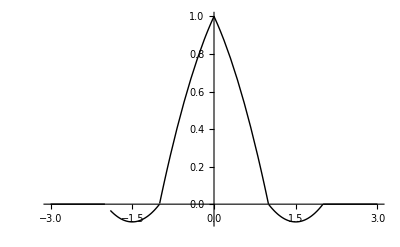

```mathematica
Sol=Sols[[1]];
FullSol=N[Join[GenSol/.Sol,Sol]]
fo[x_]:=f[x]/.FullSol;
Plot[fo[x],{x,-3,3},PlotStyle->Black,Background->White]
```